```mathematica
long[[1]]
```

{PR25,HG01104.0,m011,NA19684.1,var_chr5_83707972,var_chr5_103030947,5,83707972,103030947,11439,19.32,PUR,MXL}

```mathematica
Integrate[t^2*E^(-aa t),{t,0,Infinity}]
```

ConditionalExpression[2/aa^3,Re[aa]>0]

```mathematica
Integrate[2^2/NN^2/(1/NN+2LL)^3,{LL,0,Infinity}]
```

ConditionalExpression[1,Im[NN]≠0||Re[NN]≥0]

0.1

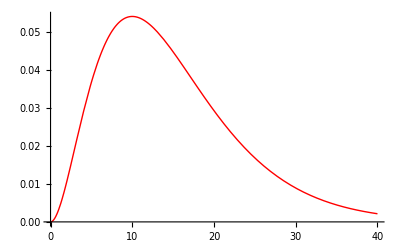

0.986246

```mathematica
(*TMRCA knowing ibd length*)
PtKl[l_,t_]:=(2 t)^2 l^3 E^(-2 t l)
(*number of switch points knowing l and t*)
PaKlt[n_,l_,t_,g_]:=If[t>g ,If[n==0,1,0]    ,  E^(-(g-t)l/2) ((g-t) l/2)^n /n!]
(*10cM segment*)
```

0.05

40

1.

{0.994474,0.00523205,0.000281593,0.0000123602,4.58934×10^-7,1.4781×10^-8,4.2061×10^-10,1.07249×10^-11,2.47794×10^-13,5.23485×10^-15,1.01882×10^-16}

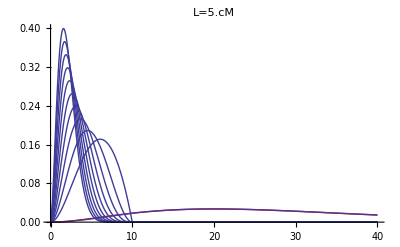

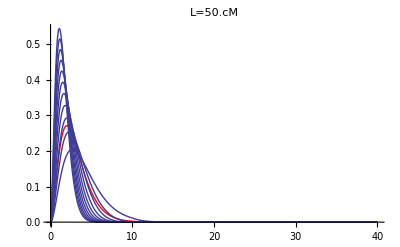

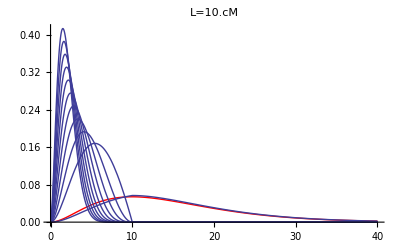

```mathematica
len=0.05
plotto=40
Uncon=Plot[PtKl[len,t],{t,0,plotto},PlotRange->All,PlotStyle->Red];
Integrate[PtKl[len,t],{t,0,1000}]
norms=Table[NIntegrate[PtKl[len,t]*PaKlt[nn,len,t,10] ,{t,0,1000}] ,{nn,0,10}] 
Show[Uncon,Plot[Table[PtKl[len,t]*PaKlt[nn,len,t,10] /norms⟦nn+1⟧ ,{nn,0,10}] ,{t,0,plotto},PlotRange->All],PlotLabel->"L="<>ToString[100len]<>"cM"]
```